```mathematica
25/Pi^2 Sum[1/n^2,{n,1,5}]
```

5269/(144 π^2)

## Pregunta 3

```mathematica
FourierTransform[Sin[b t],t,w,FourierParameters->{1,-1}]*FourierTransform[Exp[-a Abs[t]],t,w,FourierParameters->{1,-1}]
```

(2 a (-ⅈ π DiracDelta[b-w]+ⅈ π DiracDelta[b+w]))/(a^2+w^2)

```mathematica
InverseFourierTransform[(2 a (-ⅈ π DiracDelta[b-w]+ⅈ π DiracDelta[b+w]))/(a^2+w^2),w,t,FourierParameters->{1,-1}]
```

-(ⅈ a ⅇ^(-ⅈ b t) (-1+ⅇ^(2 ⅈ b t)))/(a^2+b^2)

## Pregunta 4

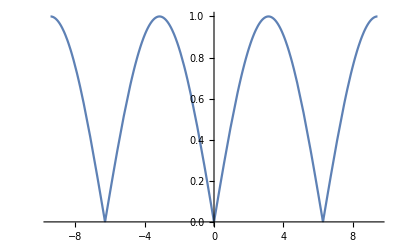

```mathematica
Plot[2/Pi+4/Pi Sum[Cos[n t]/(1-4 n^2),{n,1,100}],{t,-3Pi,3Pi}]
```

```mathematica
Sum[1/((4 n^2-1)^2),{n,1,Infinity}]
```

1/16 (-8+π^2)

## Pregunta 5

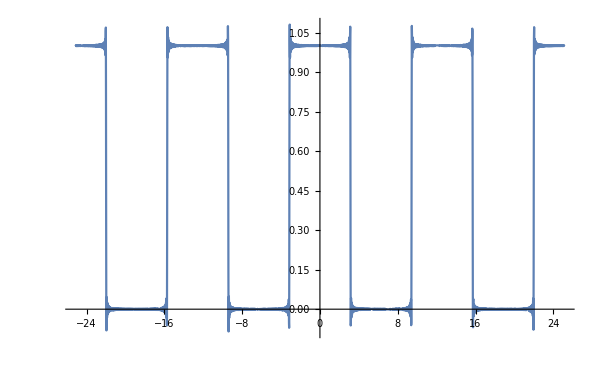

```mathematica
Plot[1/2+ 2/Pi Sum[1/n Sin[(n Pi)/2]Cos[(n t)/2],{n,1,200}],{t,-8Pi,8Pi}]
```

```mathematica
Sum[(-1)^(n+1)/(2n-1),{n,1,Infinity}]
```

π/4

```mathematica
Table[{n,Abs[2/(n Pi)Sin[(n Pi)/2]]},{n,1,7}]
```

{{1,2/π},{2,0},{3,2/(3 π)},{4,0},{5,2/(5 π)},{6,0},{7,2/(7 π)}}

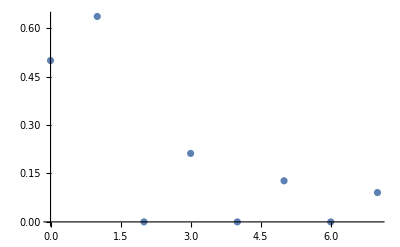

```mathematica
ListPlot[{{0,0.5},{1,2/π},{2,0},{3,2/(3 π)},{4,0},{5,2/(5 π)},{6,0},{7,2/(7 π)}}]
```

## Pregunta 6

```mathematica
FourierTransform[(1- a t)Exp[- a t]Cos[w0 t]UnitStep[t],t,w,FourierParameters->{1,-1}]
```

(ⅈ (a^2 w-w^3+w w0^2+2 ⅈ a (w^2-w0^2)))/((a^2+2 ⅈ a w-w^2+w0^2)^2)

```mathematica
Simplify[1/2 ((ⅈ (w-w0))/(a^2+2 ⅈ a (w-w0)-(w-w0)^2)+(ⅈ (w+w0))/(a^2+2 ⅈ a (w+w0)-(w+w0)^2))]
```

(ⅈ (a^2 w-w^3+w w0^2+2 ⅈ a (w^2-w0^2)))/((a^2+2 ⅈ a w-w^2+w0^2)^2)

```mathematica
(*Simplificando la expresionm con la funcion que obtuve, da lo mismo*)
```